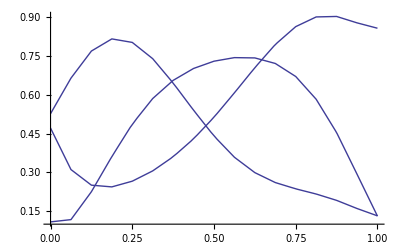

```mathematica
Plot[ColorData["Rainbow"][x]//{#[[1]],#[[2]],#[[3]]}&,{x,0,1}]
```

```mathematica
ColorData["TemperatureMap"][x]
```

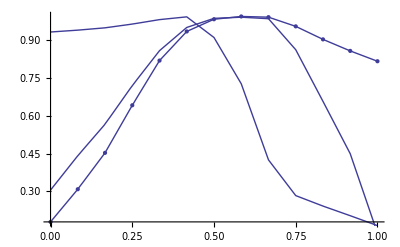

```mathematica
Show[ListPlot@((DataPaclets`ColorDataDump`getColorSchemeData["TemperatureMap"][[5,All,1]])//Transpose[{Range[0,1,1/(Length[#]-1)],#}]&),Plot[ColorData["TemperatureMap"][x]//{#[[1]],#[[2]],#[[3]]}&,{x,0,1}]]
```

```mathematica
(DataPaclets`ColorDataDump`getColorSchemeData["Rainbow"][[5]])//Transpose[{Range[0,1,1/(Length[#]-1)]//N,#[[All,1]],#[[All,2]],#[[All,3]]}]&//Dimensions
```

{17,4}

```mathematica
(DataPaclets`ColorDataDump`getColorSchemeData["Rainbow"][[5]])//Transpose[{Range[0,1,1/(Length[#]-1)]//N,#[[All,1]],#[[All,2]],#[[All,3]]}]&//ToString//CopyToClipboard
```

```mathematica
" {{0., 0.178927, 0.305394, 0.933501}, {0.0833333, 0.308746, 0.441842, 0.940894}, {0.166667, 0.453318, 0.567063, 0.950106}, {0.25, 0.642359, 0.720535, 0.964988}, {0.333333, 0.819984, 0.859297, 0.982692}, {0.416667, 0.935699, 0.951565, 0.993729}, {0.5, 0.984192, 0.987731, 0.911643}, {0.583333, 0.995282, 0.992317, 0.727853}, {0.666667, 0.992503, 0.986373, 0.425376}, {0.75, 0.955963, 0.863115, 0.283425}, {0.833333, 0.904227, 0.657999, 0.241797}, {0.916667, 0.858405, 0.449932, 0.203562}, {1., 0.817319, 0.134127, 0.164218}}"
```

```mathematica
{{0.,0.178927},{0.08333333333333333,0.308746},{0.16666666666666666,0.453318},{0.25,0.642359},{0.3333333333333333,0.819984},{0.4166666666666667,0.935699},{0.5,0.984192},{0.5833333333333334,0.995282},{0.6666666666666666,0.992503},{0.75,0.955963},{0.8333333333333334,0.904227},{0.9166666666666666,0.858405},{1.,0.817319}}
```